## Principal Component Analysis

We have seen in the lectures how Principal Component Analysis can be used to find the “most important directions” in data. Let’s try it out with a simple 2D dataset that roughly fits on a line:

```mathematica
SeedRandom[1];
```

```mathematica
data = Table[{x,3+2x+RandomVariate[NormalDistribution[0,0.6]]},{x,0,5,0.005}];
```

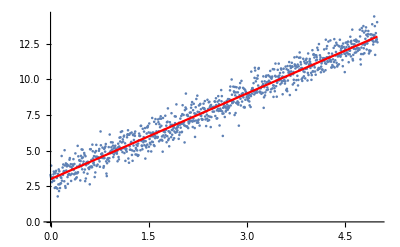

```mathematica
Show[ListPlot[data],Plot[3+2x,{x,0,5},PlotStyle->Red]]
```

```mathematica
Dimensions[data]
```

{1001,2}

In the video lectures we had the matrix of data with rows corresponding to the variables and columns corresponding to the samples (measurements of those variables). Here, we work with the standard convention in statistics and have rows for samples and columns for variables so we will need to keep in mind this different convention.

The first thing we need to do is subtract the mean in each column (i.e. standardize the data):

```mathematica
standardizedData = Standardize[data,Mean,1&];
```

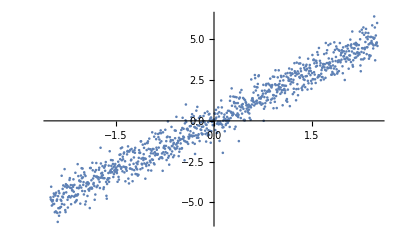

```mathematica
ListPlot[standardizedData]
```

Next we compute the singular value decomposition.

```mathematica
{U,Σ,V} = SingularValueDecomposition[standardizedData];
```

```mathematica
σs = Diagonal[Σ]
```

{103.778,8.27636}

```mathematica
Dimensions[U]
```

{1001,1001}

```mathematica
Dimensions[Σ]
```

{1001,2}

```mathematica
Dimensions[V]
```

{2,2}

```mathematica
V//MatrixForm
```

(-0.434583 | -0.900632
-0.900632 | 0.434583)

As expected, we have two singular values, one which is much larger than the other. This reflects the fact that there is much more variance along the line than orthogonal to it.

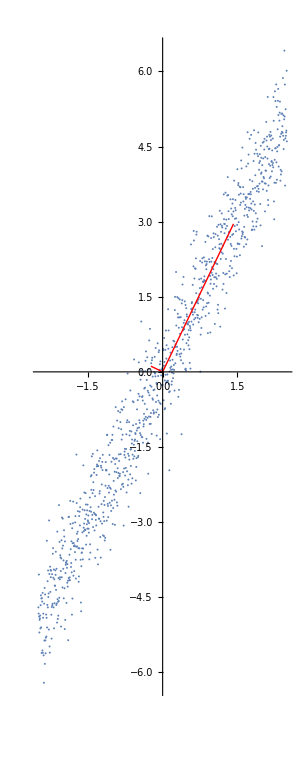

```mathematica
Show[ListPlot[standardizedData,AspectRatio->Automatic],Graphics[{Red,Thick,Line[σs[[1]]/(√(Length[data]-1)){{0,0},-V[[All,1]]}]}],Graphics[{Red,Thick,Line[σs[[2]]/(√(Length[data]-1)){{0,0},V[[All,2]]}]}],PlotRange->All]
```

The singular vectors in the columns of V give us the “most important” directions in the data

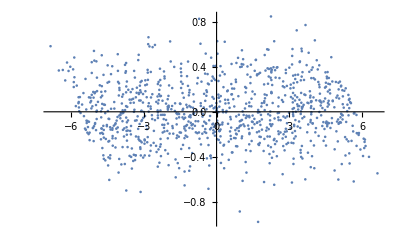

```mathematica
ListPlot[U[[All,1;;2]].Σ[[1;;2,1;;2]]]
```

The singular vectors in the columns of U give us the projection of the data long those “most important” directions (i.e. the same as standardizedData.V)

We can also directly compute this projected form of the data using PrincipalComponents

```mathematica
ListPlot[PrincipalComponents[standardizedData]]
```

-Graphics-

### In higher dimensions

Construct a 3-dimensional dataset with 3 variables:

```mathematica
data3D=Table[{x,3+2x+RandomVariate[NormalDistribution[0,0.6]],7+4x+RandomVariate[NormalDistribution[0,6]]},{x,0,5,0.005}];
```

```mathematica
ListPointPlot3D[data3D]
```

-Graphics3D-

In this case we choose to standardise by subtracting the mean and dividing by the standard deviation

Next we compute the singular value decomposition.

As expected, we have two singular values, one which is much larger than the other. This reflects the fact that there is much more variance along the line than orthogonal to it.

The singular vectors in the columns of V give us the “most important” directions in the data

The singular vectors in the columns of U give us the projection of the data long those “most important” directions (i.e. the same as standardizedData.V)

We can also directly compute this projected form of the data using PrincipalComponents

## Identifying types of flower

Let’s now use PCA to identify the type of a flower based on measurements of their properties. We will work with a dataset for three different types of iris: setosa, versicolor and virginica.

```mathematica
WolframAlpha["Iris",{{"Image:PlantData",1},"Content"}]
```

-Graphics-

The dataset is available directly through Mathematica and contains 4 variables for the length and width of the sepals and petals (in centimeters). Let’s load the data:

```mathematica
iris = ExampleData[{"MachineLearning","FisherIris"},"Data"];
```

```mathematica
iris;
```

Rearrange the data so that it is grouped by species:

```mathematica
irisbyspecies = GroupBy[iris,Last->First]
```

<|setosa→{{5.1,3.5,1.4,0.2},{4.9,3.,1.4,0.2},{4.7,3.2,1.3,0.2},{4.6,3.1,1.5,0.2},{5.,3.6,1.4,0.2},{5.4,3.9,1.7,0.4},{4.6,3.4,1.4,0.3},{5.,3.4,1.5,0.2},{4.4,2.9,1.4,0.2},{4.9,3.1,1.5,0.1},{5.4,3.7,1.5,0.2},{4.8,3.4,1.6,0.2},{4.8,3.,1.4,0.1},{4.3,3.,1.1,0.1},{5.8,4.,1.2,0.2},{5.7,4.4,1.5,0.4},{5.4,3.9,1.3,0.4},{5.1,3.5,1.4,0.3},{5.7,3.8,1.7,0.3},{5.1,3.8,1.5,0.3},{5.4,3.4,1.7,0.2},{5.1,3.7,1.5,0.4},{4.6,3.6,1.,0.2},{5.1,3.3,1.7,0.5},{4.8,3.4,1.9,0.2},{5.,3.,1.6,0.2},{5.,3.4,1.6,0.4},{5.2,3.5,1.5,0.2},{5.2,3.4,1.4,0.2},{4.7,3.2,1.6,0.2},{4.8,3.1,1.6,0.2},{5.4,3.4,1.5,0.4},{5.2,4.1,1.5,0.1},{5.5,4.2,1.4,0.2},{4.9,3.1,1.5,0.2},{5.,3.2,1.2,0.2},{5.5,3.5,1.3,0.2},{4.9,3.6,1.4,0.1},{4.4,3.,1.3,0.2},{5.1,3.4,1.5,0.2},{5.,3.5,1.3,0.3},{4.5,2.3,1.3,0.3},{4.4,3.2,1.3,0.2},{5.,3.5,1.6,0.6},{5.1,3.8,1.9,0.4},{4.8,3.,1.4,0.3},{5.1,3.8,1.6,0.2},{4.6,3.2,1.4,0.2},{5.3,3.7,1.5,0.2},{5.,3.3,1.4,0.2}},versicolor→{{7.,3.2,4.7,1.4},{6.4,3.2,4.5,1.5},{6.9,3.1,4.9,1.5},{5.5,2.3,4.,1.3},{6.5,2.8,4.6,1.5},{5.7,2.8,4.5,1.3},{6.3,3.3,4.7,1.6},{4.9,2.4,3.3,1.},{6.6,2.9,4.6,1.3},{5.2,2.7,3.9,1.4},{5.,2.,3.5,1.},{5.9,3.,4.2,1.5},{6.,2.2,4.,1.},{6.1,2.9,4.7,1.4},{5.6,2.9,3.6,1.3},{6.7,3.1,4.4,1.4},{5.6,3.,4.5,1.5},{5.8,2.7,4.1,1.},{6.2,2.2,4.5,1.5},{5.6,2.5,3.9,1.1},{5.9,3.2,4.8,1.8},{6.1,2.8,4.,1.3},{6.3,2.5,4.9,1.5},{6.1,2.8,4.7,1.2},{6.4,2.9,4.3,1.3},{6.6,3.,4.4,1.4},{6.8,2.8,4.8,1.4},{6.7,3.,5.,1.7},{6.,2.9,4.5,1.5},{5.7,2.6,3.5,1.},{5.5,2.4,3.8,1.1},{5.5,2.4,3.7,1.},{5.8,2.7,3.9,1.2},{6.,2.7,5.1,1.6},{5.4,3.,4.5,1.5},{6.,3.4,4.5,1.6},{6.7,3.1,4.7,1.5},{6.3,2.3,4.4,1.3},{5.6,3.,4.1,1.3},{5.5,2.5,4.,1.3},{5.5,2.6,4.4,1.2},{6.1,3.,4.6,1.4},{5.8,2.6,4.,1.2},{5.,2.3,3.3,1.},{5.6,2.7,4.2,1.3},{5.7,3.,4.2,1.2},{5.7,2.9,4.2,1.3},{6.2,2.9,4.3,1.3},{5.1,2.5,3.,1.1},{5.7,2.8,4.1,1.3}},virginica→{{6.3,3.3,6.,2.5},{5.8,2.7,5.1,1.9},{7.1,3.,5.9,2.1},{6.3,2.9,5.6,1.8},{6.5,3.,5.8,2.2},{7.6,3.,6.6,2.1},{4.9,2.5,4.5,1.7},{7.3,2.9,6.3,1.8},{6.7,2.5,5.8,1.8},{7.2,3.6,6.1,2.5},{6.5,3.2,5.1,2.},{6.4,2.7,5.3,1.9},{6.8,3.,5.5,2.1},{5.7,2.5,5.,2.},{5.8,2.8,5.1,2.4},{6.4,3.2,5.3,2.3},{6.5,3.,5.5,1.8},{7.7,3.8,6.7,2.2},{7.7,2.6,6.9,2.3},{6.,2.2,5.,1.5},{6.9,3.2,5.7,2.3},{5.6,2.8,4.9,2.},{7.7,2.8,6.7,2.},{6.3,2.7,4.9,1.8},{6.7,3.3,5.7,2.1},{7.2,3.2,6.,1.8},{6.2,2.8,4.8,1.8},{6.1,3.,4.9,1.8},{6.4,2.8,5.6,2.1},{7.2,3.,5.8,1.6},{7.4,2.8,6.1,1.9},{7.9,3.8,6.4,2.},{6.4,2.8,5.6,2.2},{6.3,2.8,5.1,1.5},{6.1,2.6,5.6,1.4},{7.7,3.,6.1,2.3},{6.3,3.4,5.6,2.4},{6.4,3.1,5.5,1.8},{6.,3.,4.8,1.8},{6.9,3.1,5.4,2.1},{6.7,3.1,5.6,2.4},{6.9,3.1,5.1,2.3},{5.8,2.7,5.1,1.9},{6.8,3.2,5.9,2.3},{6.7,3.3,5.7,2.5},{6.7,3.,5.2,2.3},{6.3,2.5,5.,1.9},{6.5,3.,5.2,2.},{6.2,3.4,5.4,2.3},{5.9,3.,5.1,1.8}}|>

Let’s first try to plot the data. This is a 4-dimensional dataset (one dimension for each variable) so we don’t have an easy way to visualise it all. Instead,  just visualise three dimensions by dropping one dimension

```mathematica
ListPointPlot3D[irisbyspecies[[All,All,{1,2,3}]]]
```

-Graphics3D-

It looks like there is hope for separating out the species based on their properties, but it is difficult working with 4-dimensional data. Instead, let’s project it onto the two-dimensional space spanned by the first two principal components. We do this as before: standardize the data, use the SVD to find the principal components and the projection of the data onto those components and then un-standardize the result for plotting.  Instead of doing those steps manually again, let’s use Mathematica’s DimensionReduction function which does exactly that. We tell it to use Principal Component Analysis and to project onto two dimensions

```mathematica
diris = DimensionReduction[iris[[All,1]],2,Method->"PrincipalComponentsAnalysis"]
```

DimensionReducerFunction[…]

```mathematica
irisbyspecies["setosa"][[1]]
```

{5.1,3.5,1.4,0.2}

```mathematica
diris[irisbyspecies["setosa"][[1]]]
```

{2.2647,0.480027}

The result is a DimensionReducerFunction which takes in a vector of 4 numbers and returns a vector of two numbers obtained by projecting along the two principal directions. We now apply this projection function to our iris data

```mathematica
dirisbyspecies = diris/@irisbyspecies;
```

When we plot this lower dimensional representation of the data, we can clearly delineate between the species:

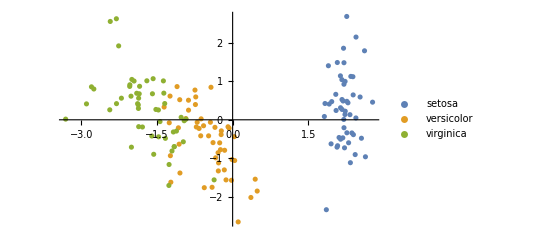

```mathematica
ListPlot[dirisbyspecies]
```

We can go even further than this. We have seen how we can use PCA to project high-dimensional data onto a lower dimensional surface, but we could also reconstruct those projected vectors in the original 4-dimensional space. For example, let’s take one sample of the setosa species:

We can project this onto the lower-dimensional space:

Then we can take these principal components and combine them with the principal component vectors to reconstruct a 4-vector in the original space. This will be the closest point on our lower-dimensional surface to the original 4-dimensional sample:

We can do these two steps (projection and reconstruction) in one go by asking for the reconstructed vector directly:

Now let’s do this for all sample points and plot the result:

Finally, we can also use this approach to fill in missing data. For example, say we had missed a measurement for our first setosa sample

We can still project this onto the lower dimensional space

And we can reconstruct a 4-dimensional vector from this, “filling in” the missing  piece:

If all we want to do is fill in the missing piece and leave the others unchanged, then we could do that too:

We won’t cover this idea further in this module, but this is a lot of information about data imputation available online.

## Handwriting recognition

We now look at another example: handwriting recognition, and in particular reading numbers. The National Institute of Standards and Technology in the US have produced a set of 60,000 handwritten numbers collected from Census Bureau employees and high school students. Let’s first load the dataset (this may take a few seconds to download the first time you run it).

This is a list of 60,000 entries, each with an image of a handwritten number and the corresponding integer label (as interpreted by a human). Take a random sample of 30 entries to get an idea of what they look like

Group the entries by the number they represent

We will just work with the zeros and ones

If we think of each 28 x 28 image as a 784 dimensional vector, then we can consider this as a set of 12,665 samples in a 784 dimensional vector space. A random vector in that space won’t look like much, but the 12,665 samples are special as they represent important “directions” in this space.

Let’s see if PCA will allow us to identify the important “directions” corresponding to zeros and ones, and even to differentiate between them. First, let’s convert the images to vectors of numbers:

Now that we have a matrix, we can use PCA to reduce the 784 dimensional vectors to just the two most important ones

Now we map our dimension reduction projection function over all of the images in our training set

If we now visualise all of those samples on our two-dimensional space, we can quite clearly distinguish between zeros and ones:

That’s all well and good, but it could be that we have just trained our model to understand the images in the training dataset we used. What if we were to throw a new, previously unseen image at it? The MNIST dataset is separated into training and testing datasets for exactly this purpose. Let’s load the test data and see how that fares

If we now visualise all of those samples on our two-dimensional space, we can quite clearly distinguish between zeros and ones:

We can also reconstruct what our model thinks a zero and a one look like:

And we can even use it to fill in missing data, as we did in the iris case: